```mathematica
(*First we curve-fit Pfail as a function of p and L, in accordance with (A1) of Watson and Barrett (2014)*)
ClearAll["Global'*"]
SetDirectory[NotebookDirectory[]];
bposd=Import["results_ToricBP+OSD.xlsx"][[1]]
bposdNames=bposd[[1]]
bposdData=bposd[[2;;]]
bposdData[[;;,1]]

mwpma=Import["results_ToricMWPMA.xlsx"][[1]];
mwpmaNames=mwpma[[1]]
mwpmaData=mwpma[[2;;]]
mwpmaData[[;;,1]]
```

{{p,L,I,varI,Pfail},{0.01,3.,0.00601687,1.6561×10^-8,0.0020493},{0.01,5.,0.00106851,2.27631×10^-9,0.0001384},{0.01,7.,0.000177853,3.02761×10^-10,0.0000111},{0.01,9.,0.0000115726,2.27529×10^-11,5.×10^-7},{0.01,11.,0.,,0.},{0.02,3.,0.0195083,4.23256×10^-8,0.008905},{0.02,5.,0.00693786,1.28044×10^-8,0.001429},{0.02,7.,0.0028631,3.30626×10^-9,0.0002256},{0.02,9.,0.000558585,7.5625×10^-10,0.0000343},{0.02,11.,0.0000796717,1.3225×10^-10,4.1×10^-6},{0.03,3.,0.037329,6.72372×10^-8,0.0210985},{0.03,5.,0.0213938,3.19983×10^-8,0.0057259},{0.03,7.,0.0125437,1.3436×10^-8,0.0015366},{0.03,9.,0.00523886,5.21284×10^-9,0.000413},{0.03,11.,0.00182087,2.12521×10^-9,0.0001265},{0.04,3.,0.0570485,8.68979×10^-8,0.0386312},{0.04,5.,0.0414823,5.66919×10^-8,0.0152435},{0.04,7.,0.0397821,3.24253×10^-8,0.005889},{0.04,9.,0.0234276,1.75873×10^-8,0.0022949},{0.04,11.,0.0108649,,0.0009457},{0.05,3.,0.0774213,9.94763×10^-8,0.0614306},{0.05,5.,0.05888,8.35881×10^-8,0.031778},{0.05,7.,0.115235,5.57942×10^-8,0.0161153},{0.05,9.,0.0703161,3.95914×10^-8,0.0084475},{0.05,11.,0.0420175,,0.0045589},{0.06,3.,0.0953458,1.04338×10^-7,0.0882586},{0.06,5.,0.0668294,1.12041×10^-7,0.0564296},{0.06,7.,0.215771,7.77191×10^-8,0.0355157},{0.06,9.,0.158252,,0.0230524},{0.06,11.,0.114998,,0.0154384}}

{p,L,I,varI,Pfail}

{{0.01,3.,0.00601687,1.6561×10^-8,0.0020493},{0.01,5.,0.00106851,2.27631×10^-9,0.0001384},{0.01,7.,0.000177853,3.02761×10^-10,0.0000111},{0.01,9.,0.0000115726,2.27529×10^-11,5.×10^-7},{0.01,11.,0.,,0.},{0.02,3.,0.0195083,4.23256×10^-8,0.008905},{0.02,5.,0.00693786,1.28044×10^-8,0.001429},{0.02,7.,0.0028631,3.30626×10^-9,0.0002256},{0.02,9.,0.000558585,7.5625×10^-10,0.0000343},{0.02,11.,0.0000796717,1.3225×10^-10,4.1×10^-6},{0.03,3.,0.037329,6.72372×10^-8,0.0210985},{0.03,5.,0.0213938,3.19983×10^-8,0.0057259},{0.03,7.,0.0125437,1.3436×10^-8,0.0015366},{0.03,9.,0.00523886,5.21284×10^-9,0.000413},{0.03,11.,0.00182087,2.12521×10^-9,0.0001265},{0.04,3.,0.0570485,8.68979×10^-8,0.0386312},{0.04,5.,0.0414823,5.66919×10^-8,0.0152435},{0.04,7.,0.0397821,3.24253×10^-8,0.005889},{0.04,9.,0.0234276,1.75873×10^-8,0.0022949},{0.04,11.,0.0108649,,0.0009457},{0.05,3.,0.0774213,9.94763×10^-8,0.0614306},{0.05,5.,0.05888,8.35881×10^-8,0.031778},{0.05,7.,0.115235,5.57942×10^-8,0.0161153},{0.05,9.,0.0703161,3.95914×10^-8,0.0084475},{0.05,11.,0.0420175,,0.0045589},{0.06,3.,0.0953458,1.04338×10^-7,0.0882586},{0.06,5.,0.0668294,1.12041×10^-7,0.0564296},{0.06,7.,0.215771,7.77191×10^-8,0.0355157},{0.06,9.,0.158252,,0.0230524},{0.06,11.,0.114998,,0.0154384}}

{0.01,0.01,0.01,0.01,0.01,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.04,0.04,0.04,0.04,0.04,0.05,0.05,0.05,0.05,0.05,0.06,0.06,0.06,0.06,0.06}

{p,L,I,varI,Pfail}

{{0.01,3.,0.00607114,1.66×10^-8,0.0020539},{0.01,5.,0.00101372,2.17×10^-9,0.0001307},{0.01,7.,0.000126092,2.34×10^-10,8.2×10^-6},{0.01,9.,0.0000296,5.37×10^-11,1.4×10^-6},{0.01,11.,2.86×10^-6,,1.×10^-7},{0.02,3.,0.0194696,4.23×10^-8,0.008902},{0.02,5.,0.00683277,1.28×10^-8,0.0014289},{0.02,7.,0.00277565,3.23×10^-9,0.0002184},{0.02,9.,0.000540757,7.34×10^-10,0.0000331},{0.02,11.,0.000100915,1.64×10^-10,5.3×10^-6},{0.03,3.,0.0370544,6.7×10^-8,0.0209569},{0.03,5.,0.020907,3.19×10^-8,0.0056916},{0.03,7.,0.0121366,1.33×10^-8,0.0015054},{0.03,9.,0.00501285,5.03×10^-9,0.0003932},{0.03,11.,0.00151189,1.81×10^-9,0.0001029},{0.04,3.,0.0573045,8.69×10^-8,0.0386647},{0.04,5.,0.0411101,5.65×10^-8,0.015139},{0.04,7.,0.0392878,3.2×10^-8,0.0057695},{0.04,9.,0.0227223,1.72×10^-8,0.0022158},{0.04,11.,0.00977385,,0.000838},{0.05,3.,0.07725,9.95×10^-8,0.0613653},{0.05,5.,0.0580166,8.36×10^-8,0.0316345},{0.05,7.,0.114961,5.57×10^-8,0.0160501},{0.05,9.,0.0681931,3.88×10^-8,0.0081399},{0.05,11.,0.0381862,,0.0040709},{0.06,3.,0.0953875,1.04×10^-7,0.0883296},{0.06,5.,0.065912,1.12×10^-7,0.0562692},{0.06,7.,0.21547,7.77×10^-8,0.0354233},{0.06,9.,0.154268,,0.0223185},{0.06,11.,0.106037,,0.0139614}}

{0.01,0.01,0.01,0.01,0.01,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.04,0.04,0.04,0.04,0.04,0.05,0.05,0.05,0.05,0.05,0.06,0.06,0.06,0.06,0.06}

{0.006020.00026,0.001070.00010,0.0001780.000035,0.00001210,0.2 √,0.01950.0004,0.006940.00023,0.002860.00012,0.000560.00006,0.0000800.000023,0.03730.0005,0.02140.0004,0.012540.00023,0.005240.00014,0.001820.00009,0.05700.0006,0.04150.0005,0.03980.0004,0.023430.00027,0.01086492 √,0.07740.0006,0.05890.0006,0.11520.0005,0.07030.0004,0.04201752 √,0.09530.0006,0.06680.0007,0.21580.0006,0.1582522 √,0.1149982 √}

{{{3.,0.006020.00026},{5.,0.001070.00010},{7.,0.0001780.000035},{9.,0.00001210},{11.,0.2 √}},{{3.,0.01950.0004},{5.,0.006940.00023},{7.,0.002860.00012},{9.,0.000560.00006},{11.,0.0000800.000023}},{{3.,0.03730.0005},{5.,0.02140.0004},{7.,0.012540.00023},{9.,0.005240.00014},{11.,0.001820.00009}},{{3.,0.05700.0006},{5.,0.04150.0005},{7.,0.03980.0004},{9.,0.023430.00027},{11.,0.01086492 √}},{{3.,0.07740.0006},{5.,0.05890.0006},{7.,0.11520.0005},{9.,0.07030.0004},{11.,0.04201752 √}},{{3.,0.09530.0006},{5.,0.06680.0007},{7.,0.21580.0006},{9.,0.1582522 √},{11.,0.1149982 √}}}

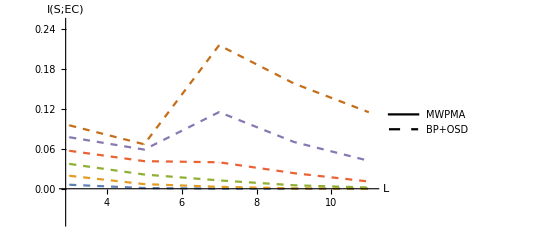

bposd-I.pdf

{0.0020490.000029,0.0001387,0.000011121,5.4.10^-7,0.,0.008900.00006,0.0014290.000024,0.0002269,0.0000344,4.11.310^-6,0.021100.00009,0.005730.00005,0.0015370.000025,0.0004130.000013,0.0001277,0.038630.00012,0.015240.00008,0.005890.00005,0.0022950.000030,0.0009460.000019,0.061430.00015,0.031780.00011,0.016120.00008,0.008450.00006,0.004560.00004,0.088260.00018,0.056430.00015,0.035520.00012,0.023050.00009,0.015440.00008}

{{{3.,0.0020490.000029},{5.,0.0001387},{7.,0.000011121},{9.,5.4.10^-7},{11.,0.}},{{3.,0.008900.00006},{5.,0.0014290.000024},{7.,0.0002269},{9.,0.0000344},{11.,4.11.310^-6}},{{3.,0.021100.00009},{5.,0.005730.00005},{7.,0.0015370.000025},{9.,0.0004130.000013},{11.,0.0001277}},{{3.,0.038630.00012},{5.,0.015240.00008},{7.,0.005890.00005},{9.,0.0022950.000030},{11.,0.0009460.000019}},{{3.,0.061430.00015},{5.,0.031780.00011},{7.,0.016120.00008},{9.,0.008450.00006},{11.,0.004560.00004}},{{3.,0.088260.00018},{5.,0.056430.00015},{7.,0.035520.00012},{9.,0.023050.00009},{11.,0.015440.00008}}}

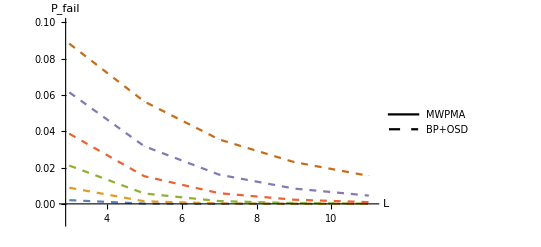

bposd-Pfail.pdf

{0.006070.00026,0.001010.00009,0.0001260.000031,0.0000300.000015,2.86×10^-62 √,0.01950.0004,0.006830.00023,0.002780.00011,0.000540.00005,0.0001010.000026,0.03710.0005,0.02090.0004,0.012140.00023,0.005010.00014,0.001510.00009,0.05730.0006,0.04110.0005,0.03930.0004,0.022720.00026,0.009773852 √,0.07730.0006,0.05800.0006,0.11500.0005,0.06820.0004,0.03818622 √,0.09540.0006,0.06590.0007,0.21550.0006,0.1542682 √,0.1060372 √}

{{{3.,0.006070.00026},{5.,0.001010.00009},{7.,0.0001260.000031},{9.,0.0000300.000015},{11.,2.86×10^-62 √}},{{3.,0.01950.0004},{5.,0.006830.00023},{7.,0.002780.00011},{9.,0.000540.00005},{11.,0.0001010.000026}},{{3.,0.03710.0005},{5.,0.02090.0004},{7.,0.012140.00023},{9.,0.005010.00014},{11.,0.001510.00009}},{{3.,0.05730.0006},{5.,0.04110.0005},{7.,0.03930.0004},{9.,0.022720.00026},{11.,0.009773852 √}},{{3.,0.07730.0006},{5.,0.05800.0006},{7.,0.11500.0005},{9.,0.06820.0004},{11.,0.03818622 √}},{{3.,0.09540.0006},{5.,0.06590.0007},{7.,0.21550.0006},{9.,0.1542682 √},{11.,0.1060372 √}}}

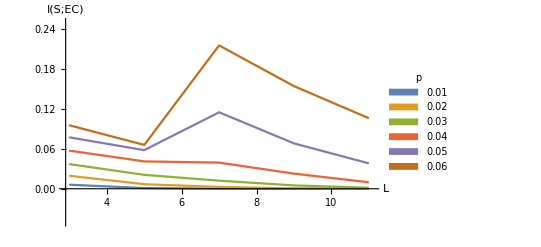

mwpma-I.pdf

{0.0020540.000029,0.0001317,8.21.810^-6,1.40.710^-6,1.02.010^-7,0.008900.00006,0.0014290.000024,0.0002189,0.0000334,5.31.510^-6,0.020960.00009,0.005690.00005,0.0015050.000025,0.0003930.000013,0.0001036,0.038660.00012,0.015140.00008,0.005770.00005,0.0022160.000030,0.0008380.000018,0.061370.00015,0.031630.00011,0.016050.00008,0.008140.00006,0.004070.00004,0.088330.00018,0.056270.00015,0.035420.00012,0.022320.00009,0.013960.00007}

{{{3.,0.0020540.000029},{5.,0.0001317},{7.,8.21.810^-6},{9.,1.40.710^-6},{11.,1.02.010^-7}},{{3.,0.008900.00006},{5.,0.0014290.000024},{7.,0.0002189},{9.,0.0000334},{11.,5.31.510^-6}},{{3.,0.020960.00009},{5.,0.005690.00005},{7.,0.0015050.000025},{9.,0.0003930.000013},{11.,0.0001036}},{{3.,0.038660.00012},{5.,0.015140.00008},{7.,0.005770.00005},{9.,0.0022160.000030},{11.,0.0008380.000018}},{{3.,0.061370.00015},{5.,0.031630.00011},{7.,0.016050.00008},{9.,0.008140.00006},{11.,0.004070.00004}},{{3.,0.088330.00018},{5.,0.056270.00015},{7.,0.035420.00012},{9.,0.022320.00009},{11.,0.013960.00007}}}

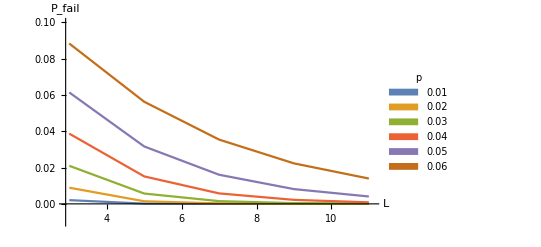

mwpma-Pfail.pdf

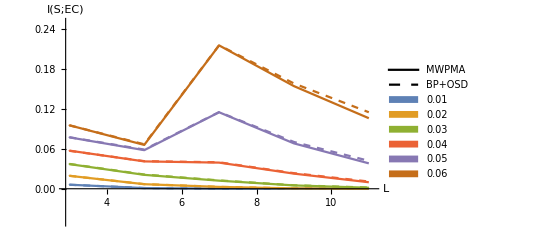

MI.pdf

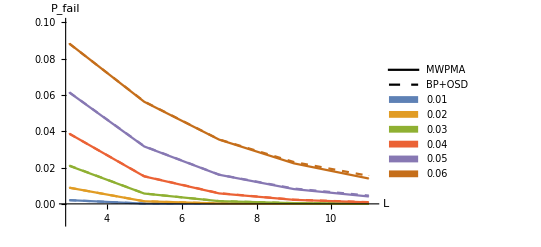

Pfail.pdf

```mathematica
Data=Apply[Around,Transpose[{bposdData[[;;,3]],2*Sqrt[bposdData[[;;,4]]]}],1]
DataPlot=Partition[Transpose[{bposdData[[;;,2]],Data}],5]
plot1=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotRange->{{2.9,11.1},{-0.05,0.25}},PlotLegends->LineLegend[{Black,{Dashed,Black}},{"MWPMA","BP+OSD"}],PlotStyle->{Dashed}]
Export["bposd-I.pdf",plot1]

Data=Apply[Around,Transpose[{bposdData[[;;,5]],2*Sqrt[bposdData[[;;,5]]*(1-bposdData[[;;,5]])/(10^7)]}],1]
DataPlot=Partition[Transpose[{bposdData[[;;,2]],Data}],5]
plot2=ListLinePlot[DataPlot,AxesLabel->{"L","P_fail"},PlotRange->{{2.9,11.1},{-0.01,0.1}},PlotLegends->LineLegend[{Black,{Dashed,Black}},{"MWPMA","BP+OSD"}],PlotStyle->{Dashed}]
Export["bposd-Pfail.pdf",plot2]

Data=Apply[Around,Transpose[{mwpmaData[[;;,3]],2*Sqrt[mwpmaData[[;;,4]]]}],1]
DataPlot=Partition[Transpose[{mwpmaData[[;;,2]],Data}],5]
plot3=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotRange->{{2.9,11.1},{-0.05,0.25}},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[bposdData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["mwpma-I.pdf",plot3]

Transpose[{mwpmaData[[;;,3]],2*Sqrt[mwpmaData[[;;,3]]]}];
Data=Apply[Around,Transpose[{mwpmaData[[;;,5]],2*Sqrt[mwpmaData[[;;,5]]*(1-bposdData[[;;,5]])/(10^7)]}],1]
DataPlot=Partition[Transpose[{mwpmaData[[;;,2]],Data}],5]
plot4=ListLinePlot[DataPlot,AxesLabel->{"L","P_fail"},PlotRange->{{2.9,11.1},{-0.01,0.1}},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[bposdData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["mwpma-Pfail.pdf",plot4]

plot5 =Show[plot1,plot3]
Export["MI.pdf",plot5]

plot6 =Show[plot2,plot4]
Export["Pfail.pdf",plot6]
```